## SRLG without depletion

```mathematica
RangeΦ=Range[0,1,0.1];
```

### Parameters

```mathematica
Nm=12;
Clear[Nm]
```

```mathematica
X[J_,μ_]:=1/2(J+μ);
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√(Sinh[X[J,μ]]^2+Exp[-J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√(Sinh[X[J,μ]]^2+Exp[-J]))
```

### Correlation length

```mathematica
ξ[J_,μ_] := Log[λp[J,μ]/λm[J,μ]]^-1;
```

```mathematica
N[ξ[5,-5]]
```

6.07754

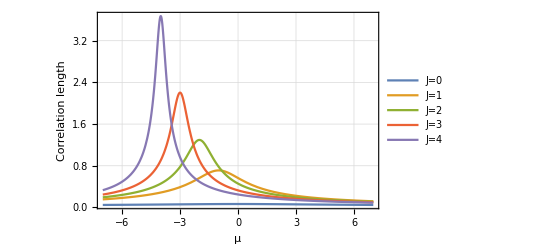

```mathematica
Plot[Evaluate[Table[ξ[J,μ],{J,0.000001,5}]],{μ,-7,7},PlotRange->All,Frame->True,GridLines->Automatic,FrameLabel->{"μ","Correlation length"}, PlotLegends->{"J=0","J=1", "J=2","J=3","J=4"}]
```

```mathematica
Table[Limit[ξ[J,μ],J-> ∞],{μ,-7,7}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[Limit[ξ[J,μ],J->0],{μ,-7,7}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

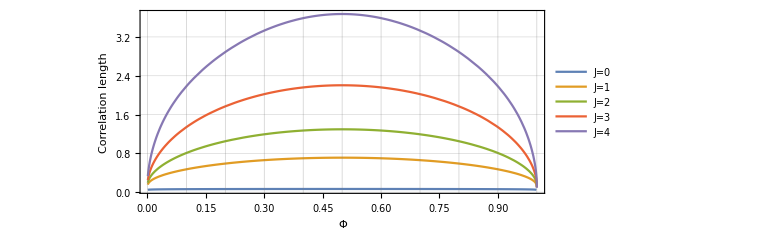

```mathematica
ParametricPlot[Evaluate[Table[{Φ[J,μ,12],ξ[J,μ]},{J,0.000001,5}]],{μ,-7,7},PlotRange->All,Frame->True,GridLines->{RangeΦ,Automatic},FrameLabel->{"Φ","Correlation length"}, PlotLegends->{"J=0","J=1", "J=2","J=3","J=4"},AspectRatio->2/5,ImageSize->Large,LabelStyle->{12,GrayLevel[0]}]
```

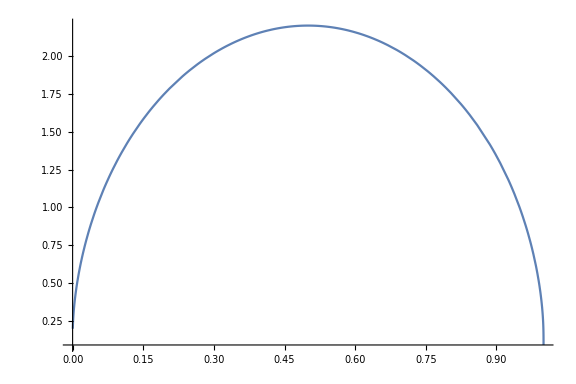

```mathematica
ParametricPlot[{{Φ[3,μ,12],ξ[3,μ]}},{μ,-8,8},ImageSize->Large,AspectRatio->2/3,PlotRange->Full]
```

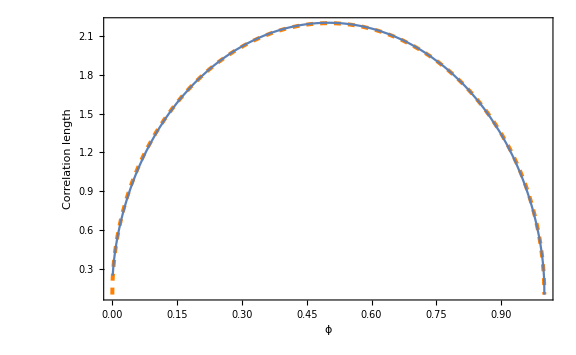

```mathematica
Show[Plot[0.1+(2.1/ArcTanh[-0.5(0.5-1)]^(1/2))ArcTanh[-x(x-1)]^(1/2),{x,0,1},PlotRange->Full,Frame->True,ImageSize->Large,PlotStyle->{Thickness[0.005],Dashed,RGBColor[1,0.5,0]},FrameLabel->{"ϕ","Correlation length"},LabelStyle->{12,GrayLevel[0]}],ParametricPlot[{{Φ[3,μ,12],ξ[3,μ]}},{μ,-7,7},ImageSize->Large,PlotRange->Full]]
```

## Average occupation

```mathematica
Φ[J_,μ_,Nm_]:= 1/2(1 + Tanh[Nm/(2ξ[J,μ])] Sinh[X[J,μ]]/(√(Sinh[X[J,μ]]^2+ Exp[-J])) );
```

```mathematica
Φp1[J_,μ_,Nm_]:= 1/2(1 + ((λp^Nm-λm^Nm)/(λp^Nm+λm^Nm))^ Sinh[X[J,μ]]/(√(Sinh[X[J,μ]]^2+ Exp[-J])) )
```

```mathematica
FullSimplify[Φp1[J,μ,Nm]^2]
```

1/4 (1+((1-(2 λm^Nm)/(λm^Nm+λp^Nm))^Null Sinh[(J+μ)/2])/(√(ⅇ^-J+Sinh[(J+μ)/2]^2)))^2

```mathematica
Φ[0.0000000001,-2,13]*13
```

1.54964

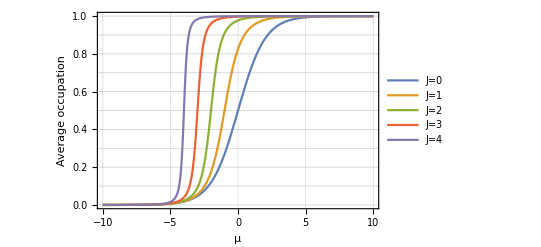

```mathematica
Plot[Evaluate[Table[{Φ[J,μ,10000]},{J,0.000001,5}]],{μ,-10,10},PlotRange->All,Frame->True,GridLines->{Automatic,RangeΦ},FrameLabel->{"μ","Average occupation"}, PlotLegends->{"J=0","J=1", "J=2","J=3","J=4"}]
```

```mathematica
ΦLT[J_,μ_] := 1/2(1 + Sinh[X[J,μ]]/(√(Sinh[X[J,μ]]^2+ Exp[-J])) )
```

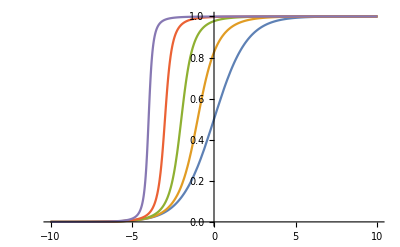

```mathematica
Plot[Evaluate[Table[{ΦLT[J,μ]},{J,0.000001,5}]],{μ,-10,10}]
```

### Average square occupation

```mathematica
Φ2[J_,μ_,Nm_]:= 1/4(1 + Sinh[X[J,μ]]^2/(Sinh[X[J,μ]]^2+Exp[-J])+Tanh[Nm/(2ξ[J,μ])]((2Sinh[X[J,μ]])/(√(Sinh[X[J,μ]]^2+Exp[-J]))+1/Nm (Exp[-J]Cosh[X[J,μ]])/((Sinh[X[J,μ]]^2+Exp[-J])^(3/2))));
```

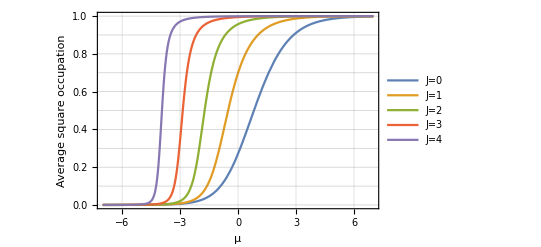

```mathematica
Plot[Evaluate[Table[{Φ2[J,μ,12]},{J,0.000001,5}]],{μ,-7,7},PlotRange->All,Frame->True,GridLines->{Automatic,RangeΦ},FrameLabel->{"μ","Average square occupation"}, PlotLegends->{"J=0","J=1", "J=2","J=3","J=4"}]
```

### Variance and standard deviation

```mathematica
σ2[J_,μ_,Nm_] := Φ2[J,μ,Nm]-Φ[J,μ,Nm]^2;
σ[J_,μ_,Nm_]:=√(Φ2[J,μ,Nm]-Φ[J,μ,Nm]^2);
```

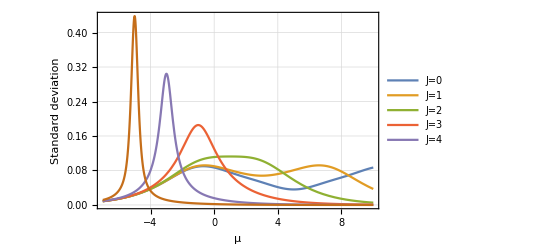

```mathematica
Plot[Evaluate[Table[σ[J,μ,12],{J,-5,5,2}]],{μ,-7,10},PlotRange->Full,Frame->True,GridLines->{Automatic,Automatic},FrameLabel->{"μ","Standard deviation"}, PlotLegends->{"J=0","J=1", "J=2","J=3","J=4"}]
```

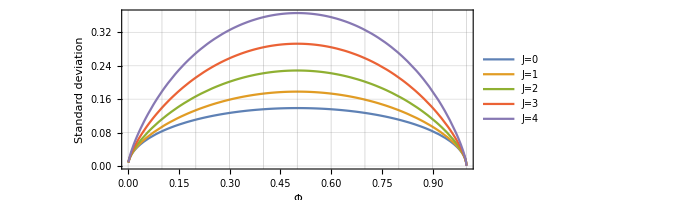

```mathematica
ParametricPlot[Evaluate[Table[{Φ[J,μ,13],σ[J,μ,13]},{J,0.000001,5}]],{μ,-7,7},PlotRange->Full,Frame->True,GridLines->{RangeΦ,Automatic},FrameLabel->{"Φ","Standard deviation"}, PlotLegends->{"J=0","J=1", "J=2","J=3","J=4"}]
```

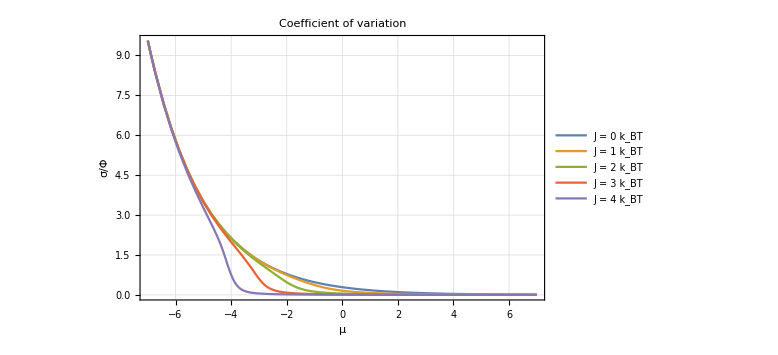

```mathematica
Plot[Evaluate[Table[σ[J,μ,12]/Φ[J,μ,12],{J,0.000001,5}]],{μ,-7,7},PlotRange->Full,Frame->True,GridLines->{Automatic,Automatic},FrameLabel->{"μ","σ/Φ"}, PlotLegends->Placed[LineLegend[{"J = 0 k_BT","J = 1 k_BT","J = 2 k_BT","J = 3 k_BT","J = 4 k_BT"},LegendFunction->Frame],{{0.9,0.5},{0.7,0.5}}],ImageSize->Large,LabelStyle->{GrayLevel[0],12},PlotLabel->"Coefficient of variation"]
```

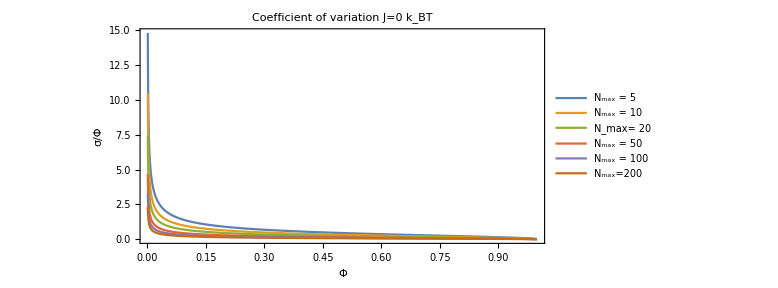

```mathematica
ParametricPlot[Evaluate[Table[{Φ[0.00001,μ,Nm],σ[0.00001,μ,Nm]/Φ[0.000001,μ,Nm]},{Nm,{5,10,20,50,100,200}}]],{μ,-7,7},PlotRange->Full,Frame->True,FrameLabel->{"Φ","σ/Φ"}, PlotLegends->Placed[LineLegend[{"N_max = 5","N_max = 10","N_max= 20","N_max = 50","N_max = 100","N_max=200"},LegendFunction->Frame],{{0.9,0.5},{0.7,0.5}}],AspectRatio->1/2,ImageSize->Large,LabelStyle->{GrayLevel[0],12},PlotLabel->"Coefficient of variation J=0 k_BT"]
```

### Relaxation time

```mathematica
τ[J_]:=Exp[J/2]/2;
τe[J_]:= 1/2 Exp[J];
```

```mathematica
τp[J_]:= 1/(1-Tanh[J/2]);
```

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Data0 = Import["/home/mariajose/Escritorio/Simulations/Without depletion/Glauber/RelaxTimes/ResTime_J=-mu.dat"];
Data1 = Import["/home/mariajose/Escritorio/Simulations/Without depletion/Glauber/RelaxTimes/StallTime_J=-mu.dat"];
Data2 = Import["/home/mariajose/Escritorio/Simulations/Without depletion/Relaxation times/ResTime_6.dat"];
Data3 = Import["/home/mariajose/Escritorio/Simulations/Without depletion/Relaxation times/StallTime_6.dat"];
Data4 = Import["/home/mariajose/Escritorio/Simulations/Without depletion/Fred Dynamics/Relaxation times/ResTime_6.dat"];
Data5 = Import["/home/mariajose/Escritorio/Simulations/Without depletion/Fred Dynamics/Relaxation times/StallTime_6.dat"];
```

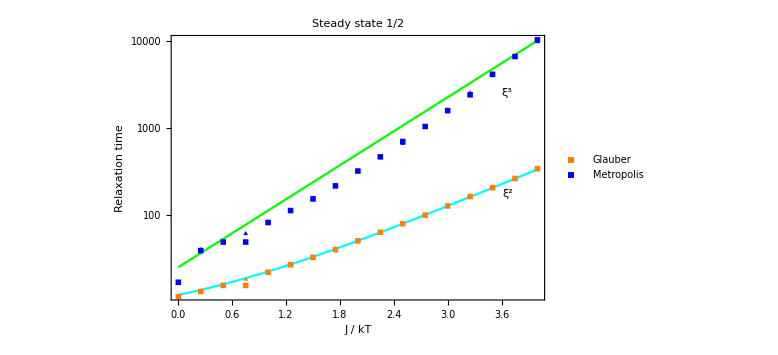

```mathematica
Show[LogPlot[{12*τp[J],1/2*50* Exp[3 J/2]},{J,0,4},ImageSize->Large,Frame->True,FrameLabel->{"J / kT","Relaxation time"},LabelStyle->{12,GrayLevel[0]},PlotLabel->"Steady state 1/2",PlotStyle->{Cyan,Green},PlotLegends->{Placed["ξ^2",{{0.9,0.4},{0.7,0.5}}],Placed["ξ^3",{{0.9,0.8},{0.7,0.8}}]}],ListLogPlot[{Data0[[All,{1,2}]],Data1[[All,{1,2}]],Data2[[All,{1,2}]],Data3[[All,{1,2}]]},PlotMarkers-> {{■,20},{▲,20}},PlotStyle -> {Orange,Orange, Blue,Blue},PlotLegends->{"Glauber",None,"Metropolis",None}]]
```

```mathematica
Export["/home/mariajose/Escritorio/Mathematica/Plots/RelaxTime/M_vs_G_05_Log.png",%17]
```

/home/mariajose/Escritorio/Mathematica/Plots/RelaxTime/M_vs_G_05_Log.png

```mathematica
Manipulate[Show[LogPlot[{1/2 b Exp[a J/2],1/2 d Exp[c J/2],1/2g Exp[f J/2]},{J,0,4},ImageSize->Large,Frame->True,FrameLabel->{"J / kT","Relaxation time"},LabelStyle->{12,GrayLevel[0]}],ListLogPlot[{Data0[[All,{1,2}]],Data1[[All,{1,2}]],Data2[[All,{1,2}]],Data3[[All,{1,2}]],Data4[[All,{1,2}]],Data5[[All,{1,2}]]}]],{a,0,5},{b,0,20},{c,0,5},{d,0,50},{f,0,5},{g,0,50}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLogPlot::lpn: {{{-1.5,-1.70513},{-1.,-1.31768},{-0.5,-0.978645},{0.,-0.696762},{0.5,-0.477556},{1.,-0.316957},{1.5,-0.205342},{2.,-0.130887},{2.5,-0.0827935},{3.,-0.0525378},{3.5,-0.0336944},{4.,-0.0220553},{4.5,-0.0149502},{5.,-0.0105933}},{{-2.75,-2.61273},{-2.5,-2.32995},«11»,{0.5,-0.105962}},{«1»},«1»,{«1»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
Manipulate[Show[LogPlot[a Exp[b J],{J,0,4},ImageSize->Large,Frame->True,FrameLabel->{"J / kT","Relaxation time"},LabelStyle->{12,GrayLevel[0]}],ListLogPlot[{Data0[[All,{1,2}]],Data1[[All,{1,2}]]}]],{a,1,200},{b,0,5}]
```

```mathematica
Manipulate[Plot[a ξ[J,-J]^b,{J,0,8}],{a,1,20},{b,0,3}]
```